```mathematica
r12 := (r2 - a2  Exp[I ϕ1])/(1-r2   a2  Exp[I ϕ1])
trans:=(r1 - r12 a1  Exp[I ϕ1])/(1-r1  r12  a1  Exp[I ϕ1])
```

```mathematica
n:=3.45;
c := 299792458;
R1:=10 10^(-6);
R2:=10 10^(-6);
d1:= 2 Pi R1
d2:= 2 Pi R2
λ:=1550 10^(-9); (* resonant wavelength *)
Q1:=1×10^5;
Q2:=1×10^6;
g1 := 1 5
g2 :=30
α1:=(2 Pi n)/(λ  Q1) (*139.85*)
α2:=(2 Pi n)/(λ  Q2) (*13.985*)
a1:= Exp[-(α1-g1 ) d1/2]
a2:= Exp[-(α2-g2) d2/2]
t1:=√(1-r1^2)
t2:=√(1-r2^2)
r1:= 0.79998
r2:= 0.9999
```

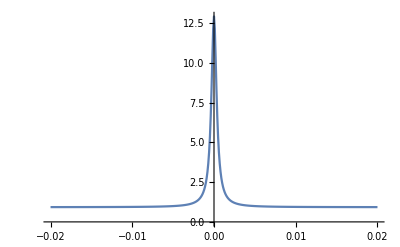

```mathematica
ϕ1min:=-0.02;
ϕ1max:=0.02;
transdata:=Table[{ϕ1,Abs[trans]^2},{ϕ1,ϕ1min, ϕ1max, 0.0001}]
ListLinePlot[transdata,PlotRange->All]
```

```mathematica
ϕ12 := ArcTan[(a2(r2^2 -1)  Sin[ϕ1])/((a2^2+1)r2-a2 (r2^2 +1)Cos[ϕ1])]   (*-ArcTan[(a2  Sin[ϕ1])/(r2-a2 Cos[ϕ1])] + ArcTan[(r2 a2  Sin[ϕ1])/(1- r2 a2 Cos[ϕ1])]*)
ϕeff := ArcTan[(a1 Abs[r12] (r1^2 -1)Sin[ϕ1 + ϕ12])/(a1^2 Abs[r12]^2 r1-a1 Abs[r12](r1^2 +1) Cos[ϕ1 + ϕ12] +r1)]
vg := (n/c) ((a1 (-1+r1^2) Abs[r12] (-a1 (1+r1^2) Abs[r12]+r1 Cos[ϕ1+ϕ12]+a1^2 r1 Abs[r12]^2 Cos[ϕ1+ϕ12]))/((r1^2+a1^2 Abs[r12]^2-2 a1 r1 Abs[r12] Cos[ϕ1+ϕ12]) (1+a1^2 r1^2 Abs[r12]^2-2 a1 r1 Abs[r12] Cos[ϕ1+ϕ12])))
```

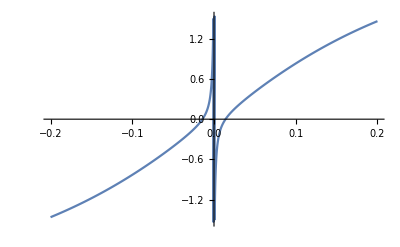

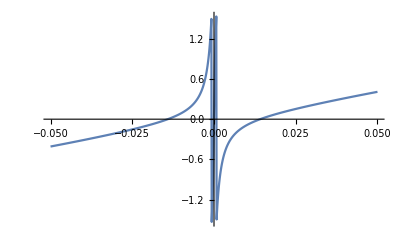

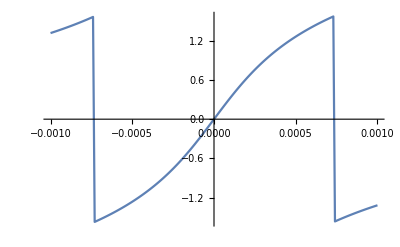

```mathematica
ϕ1min:=-0.2;
ϕ1max:=0.2;
phasedata1:=Table[{ϕ1,ϕeff},{ϕ1,ϕ1min, ϕ1max, 0.0001}]
ListLinePlot[phasedata1,PlotRange->All]
phasedata2:=Table[{ϕ1,ϕeff},{ϕ1,-0.05, 0.05, 0.0001}]
ListLinePlot[phasedata2,PlotRange->All]
phasedata2:=Table[{ϕ1,ϕeff},{ϕ1,-0.001, 0.001, 0.00001}]
ListLinePlot[phasedata2,PlotRange->All]
```

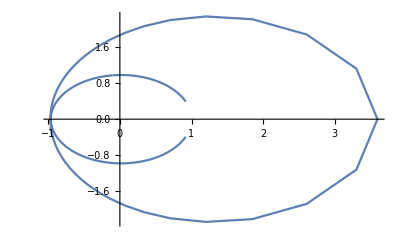

```mathematica
phasordata:=Table[{Re[trans],Im[trans]},{ϕ1,-1, 1, 0.0001}]
ListLinePlot[phasordata,PlotRange->All]
```

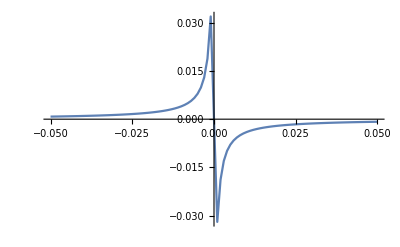

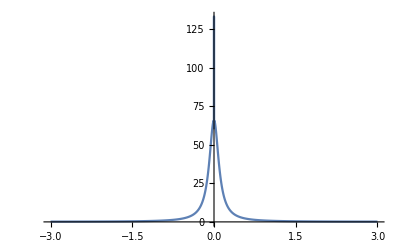

```mathematica
ϕ1min:=-0.05;
ϕ1max:=0.05
phase12data:=Table[{ϕ1,ϕ12},{ϕ1,ϕ1min, ϕ1max, 0.001}]
ListLinePlot[phase12data,PlotRange->All]
groupindexdata:=Table[{ϕ1,c vg},{ϕ1,-3.0, 3.0, 0.001}]
ListLinePlot[groupindexdata,PlotRange->All]
```

```mathematica
r1 - Abs[r12]a1 /. ϕ1->0
r1 - r2 a1 /. ϕ1->0
r2 - a2 /. ϕ1->0
```

-0.473394

-0.0956169

-0.000231883

```mathematica
(1/vg) /. ϕ1->0
(c vg) /. ϕ1->0
```

-3.70759×10^7

-8.0859